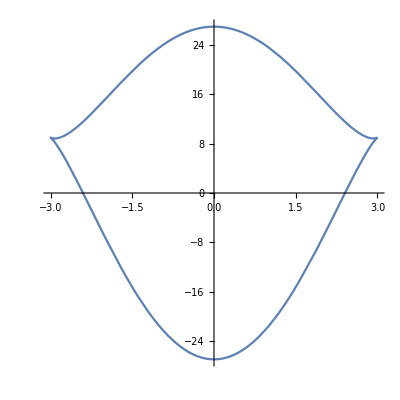

```mathematica
InputSignal[t_]:=3Cos[t];
damp[x_]:=x^2;
spring[x_]:=x;
Hysteresis[t_]:={InputSignal[t],spring[InputSignal[t]]*InputSignal[t]+damp[InputSignal'[t]]*InputSignal'[t]}
ParametricPlot[Hysteresis[t],{t,0,2π},AspectRatio->1]
```